{73/2,27,23/2,17/2,0,1/2,7/2,0,34}

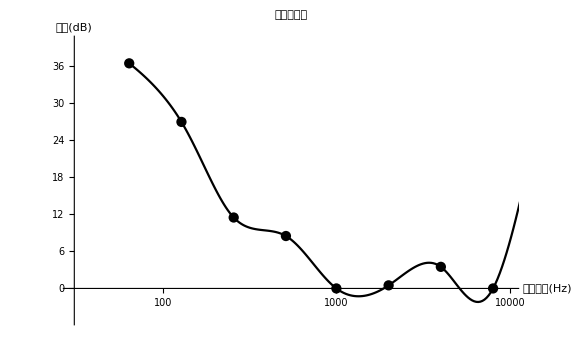

```mathematica
louda = {31, 24, 7, 5, -3, -3, -1, -4,30};
loudb = {34, 22, 8, 4, -5, -4, -0, -4,30};
loud = (louda + loudb) / 2;
std = (-3 -5) / 2;
loud = loud - std
freq = {64, 128, 256, 512, 1000, 2000, 4000, 8000,16000};
freqnew = Map[Log[E,#]&,freq];
fitData = Transpose[{freq, loud}];


Show[ListLogLinearPlot[fitData,Joined->True,InterpolationOrder->3,PlotRange->{{30,10000},{-5,40}},PlotStyle->Black],
ListLogLinearPlot[fitData,PlotStyle->Black],
AxesLabel->{Style["声音频率(Hz)",15,Bold],Style["声强(dB)",15,Bold]},
PlotLabel->Style["听阈曲线图",18,FontFamily->"Hack Nerd Font",Bold],
ImageSize->Large]
```

```mathematica
{73/2,27,23/2,17/2,0,1/2,7/2,0}
```

{73/2,27,23/2,17/2,0,1/2,7/2,0}